## Preprocessing for Chi + case

```mathematica
(* importing images for Ecadherin signal *)
```

```mathematica
dir="C:\\Users\\aliha\\Desktop\\research related\\raw data\\@96 hours\\chi pos\\";
filenames=Flatten@StringCases[Import[dir],__~~"TxRed"~~__~~".tif"];
ordering=Ordering@*Flatten@Map[StringCases[#,x__~~"\\"~~___:>ToExpression@x]&,filenames];
filenames=filenames[[ordering]];
images=ImageAdjust@Import[dir<>#]&/@filenames;
```

```mathematica
(* correction for uneven illumination *)
```

```mathematica
imgBrightnessCorr=BrightnessEqualize/@images;
```

```mathematica
hist=ImageHistogram[#,InterpolationOrder->3,Filling->None,
PlotStyle->XYZColor[0,0,0,0.25]]&/@imgBrightnessCorr;
```

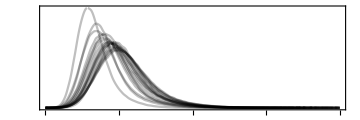

```mathematica
Show[hist,PlotRange-> All,ImageSize-> Medium]
```

```mathematica
(* mean and std of intensities *)
```

```mathematica
histStats=Function[hist,Block[{histdata},
histdata=Flatten[Cases[Unevaluated[hist],Line[x__]:> x,Infinity],1];
{Mean@#,StandardDeviation@#}&@WeightedData[Sequence@@Thread[histdata]]
],Listable][hist];
```

```mathematica
MapIndexed[#2[[1]]->#1&,histStats]
```

{1→{0.25493,0.0878899},2→{0.164982,0.057825},3→{0.226023,0.0763113},4→{0.227607,0.0858769},5→{0.244455,0.0881388},6→{0.255035,0.0929188},7→{0.200866,0.0766978},8→{0.265451,0.0847487},9→{0.196779,0.0687499},10→{0.219965,0.0802532},11→{0.270945,0.0914183},12→{0.25115,0.086045},13→{0.270802,0.0894233},14→{0.234096,0.0847527},15→{0.249995,0.0867049},16→{0.25458,0.0837057},17→{0.265975,0.0907212},18→{0.275521,0.0954158},19→{0.276594,0.0944412}}

```mathematica
{mean,std}=Thread[histStats];
```

```mathematica
(* thresholding image *)
```

```mathematica
imagesMinNoise=MapThread[
{ecad,μ,σ}↦Clip[ImageSubtract[ecad,(μ-σ)],{0.,1.}],
{imgBrightnessCorr,mean,std}];
```

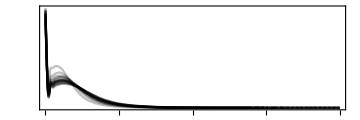

```mathematica
Show[ImageHistogram[#,InterpolationOrder->3,Filling->None,
PlotStyle->XYZColor[0,0,0,0.25]]&/@imagesMinNoise,PlotRange-> All,
ImageSize-> Medium]
```

```mathematica
(* setting reference image for histogram matching *)
```

```mathematica
reference=imagesMinNoise[[5]];
imagesCorr=HistogramTransform[#,reference]&/@Delete[imagesMinNoise,5];
imagesCorr= Insert[imagesCorr,reference,5];
```

```mathematica
Length[imagesCorr]==Length[filenames]
```

True

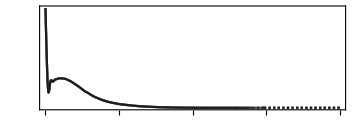

```mathematica
Show[
ImageHistogram[#,InterpolationOrder->3,Filling->None,PlotStyle->XYZColor[0,0,0,0.1]]&/@imagesCorr,
PlotRange->All,ImageSize-> Medium]
```

```mathematica
(* after processing *)
```

```mathematica
Rasterize[Grid[(imagesCorr~Partition~9),Frame->True],"Image"]
```

-Graphics-

```mathematica
(* prior processing *)
```

```mathematica
Rasterize[Grid[(images~Partition~9),Frame->True],"Image"]
```

-Graphics-

```mathematica
(* Scan[Export[dir<>ToString@#<>"\\imagecorrMinusMean"<>ToString@#<>".tiff", imagesCorr[[#]] ]&,Range[Length@images]]*)
```

## Preprocessing for Chi -ve case

```mathematica
(* importing images for Ecadherin signal *)
```

```mathematica
dir="C:\\Users\\aliha\\Desktop\\research related\\raw data\\@96 hours\\chi neg\\";
filenames=Flatten@StringCases[Import[dir],__~~"TxRed"~~__~~".tif"];
ordering=Ordering@Flatten@Map[StringCases[#,x__~~"\\"~~___:>ToExpression@x]&,filenames];
filenames=filenames[[ordering]];
images=ImageAdjust@Import[dir<>#]&/@filenames;
```

```mathematica
(* correction for uneven illumination *)
```

```mathematica
imgBrightnessCorr=BrightnessEqualize/@images;
```

```mathematica
hist=ImageHistogram[#,InterpolationOrder->3,Filling->None,
PlotStyle->XYZColor[0,0,0,0.25]]&/@imgBrightnessCorr;
```

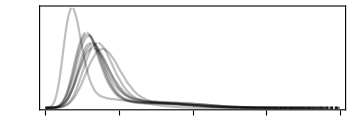

```mathematica
Show[hist,PlotRange-> All,ImageSize-> Medium]
```

```mathematica
(* mean and std of image intensity *)
```

```mathematica
histStats=Function[hist,Block[{histdata},
histdata=Flatten[Cases[Unevaluated[hist],Line[x__]:> x,Infinity],1];
{Mean@#,StandardDeviation@#}&@WeightedData[Sequence@@Thread[histdata]]
],Listable][hist];
```

```mathematica
MapIndexed[#2[[1]]->#1&,histStats]
```

{1→{0.220351,0.118299},2→{0.215945,0.0950098},3→{0.185264,0.0954239},4→{0.215123,0.116633},5→{0.191752,0.102692},6→{0.129004,0.0782769},7→{0.186039,0.105758},8→{0.212143,0.115329},9→{0.226427,0.0925879}}

```mathematica
{mean,std}=Thread[histStats];
```

```mathematica
(* thresholding image *)
```

```mathematica
imagesMinNoise=MapThread[
Function[{ecad,μ,σ},Clip[ImageSubtract[ecad,(μ-σ)],{0.,1.}]],
{imgBrightnessCorr,mean,std}];
```

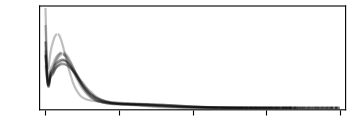

```mathematica
Show[ImageHistogram[#,InterpolationOrder->3,Filling->None,
PlotStyle->XYZColor[0,0,0,0.25]]&/@imagesMinNoise,PlotRange-> All,
ImageSize-> Medium]
```

```mathematica
(* setting reference image for histogram matching *)
```

```mathematica
reference=First[imagesMinNoise];
imagesCorr=HistogramTransform[#,reference]&/@Delete[imagesMinNoise,1];
imagesCorr=Insert[imagesCorr,reference,1];
```

```mathematica
Length[imagesCorr]==Length[filenames]
```

True

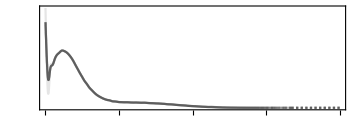

```mathematica
Show[
ImageHistogram[#,InterpolationOrder->3,Filling->None,PlotStyle->XYZColor[0,0,0,0.1]]&/@imagesCorr,
PlotRange->All,ImageSize-> Medium]
```

```mathematica
(* after processing *)
```

```mathematica
Rasterize[Grid[(imagesCorr~Partition~9),Frame->True],"Image"]
```

-Graphics-

```mathematica
(* prior processing *)
```

```mathematica
Rasterize[Grid[(images~Partition~9),Frame->True],"Image"]
```

-Graphics-

```mathematica
(* Scan[Export[dir<>ToString@#<>"\\imagecorrMinusMean"<>ToString@#<>".tiff", imagesCorr[[#]] ]&, Range[Length@imagesCorr]] *)
```

## background noise for both cases post treatment

```mathematica
(* checking background noise for both aggregates *)
```

```mathematica
{bgmaskpos,bgmaskneg}={-Graphics-,-Graphics-};
```

```mathematica
With[{bgmaskpos=bgmaskpos,bgmaskneg=bgmaskneg},
bgCheck[img1_,img2_]:= Module[{bgpos,bgneg,ind},
{bgpos,bgneg}={PixelValue[Import@img1,bgmaskpos],PixelValue[Import@img2,bgmaskneg]};
ind=Min[Length/@{bgpos,bgneg}];
Print@ListPlot[{bgpos[[;;ind]],bgneg[[;;ind]]},
PlotStyle->{Directive[Red,Opacity[0.25]],Directive[Blue,Opacity[0.25]]},ImageSize->Small];
Mean/@{bgpos,bgneg}
]
];
```

```mathematica
(* when no threshold is applied, only illumination correction and histogram matching *)
```

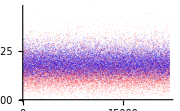

{0.15663,0.190118}

```mathematica
bgCheck["C:\\Users\\aliha\\Desktop\\research related\\raw data\\@96 hours\\chi pos\\3\\imagecorr3.tiff",
"C:\\Users\\aliha\\Desktop\\research related\\raw data\\@96 hours\\chi neg\\1\\imagecorr1.tiff"]
```

```mathematica
(* when μ - σ is subtracted from the signal  *)
```

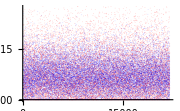

{0.0718456,0.0725155}

```mathematica
bgCheck["C:\\Users\\aliha\\Desktop\\research related\\raw data\\@96 hours\\chi pos\\3\\imagecorrMinusSigma3.tiff",
"C:\\Users\\aliha\\Desktop\\research related\\raw data\\@96 hours\\chi neg\\1\\imagecorrMinusSigma1.tiff"]
```

```mathematica
(* when μ is subtracted from the signal  *)
```

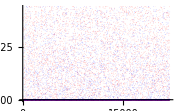

{0.0180223,0.00446901}

```mathematica
bgCheck["C:\\Users\\aliha\\Desktop\\research related\\raw data\\@96 hours\\chi pos\\3\\imagecorrMinusMean3.tiff",
"C:\\Users\\aliha\\Desktop\\research related\\raw data\\@96 hours\\chi neg\\1\\imagecorrMinusMean1.tiff"]
```

## signal post treatment

```mathematica
(*
a line passing through the aggregate:
  (1) with background
(2) removal of μ - σ
(3) signal minus μ
*)
```

```mathematica
signalCheck[file_]:=ImageData[Import@file][[530;;534]]//ListPlot[#,Joined->True,PlotStyle->XYZColor[0,0,0,0.20],ImageSize->Small]&;
```

```mathematica
(* 1 *)
```

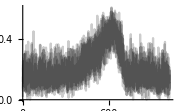

```mathematica
signalCheck["C:\\Users\\aliha\\Desktop\\research related\\raw data\\@96 hours\\chi pos\\3\\imagecorr3.tiff"]
```

```mathematica
(* 2 *)
```

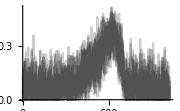

```mathematica
signalCheck["C:\\Users\\aliha\\Desktop\\research related\\raw data\\@96 hours\\chi pos\\3\\imagecorrMinusSigma3.tiff"]
```

```mathematica
(* 3 *)
```

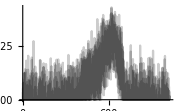

```mathematica
signalCheck["C:\\Users\\aliha\\Desktop\\research related\\raw data\\@96 hours\\chi pos\\3\\imagecorrMinusMean3.tiff"]
```